```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210224_impacts_in_time_windows"];
```

```mathematica
datafull43=Import["ccm1_data_modified_numbered_slx.mx"];
datafull=Import["../data/ccm1_data_modified.csv",HeaderLines->1];
```

```mathematica
Dimensions@datafull43
Dimensions@datafull
```

{459201,16}

{459203,16}

```mathematica
nonzerothicknesspos=Position[datafull[[All,10]],x_/;!TrueQ[x==0],{1},Heads->False];
```

```mathematica
nonNAthicknesspos=Position[datafull[[All,10]],x_/;!TrueQ[x=="NA"],{1},Heads->False];
```

```mathematica
nonzeroandNAthicknessposs=Intersection[nonzerothicknesspos,nonNAthicknesspos];
```

```mathematica
datafullwiththicknonzero=datafull[[Flatten@nonzeroandNAthicknessposs,All]];
```

```mathematica
Dimensions@datafullwiththicknonzero (*zeros are 13% of the whole data*)
```

{397860,16}

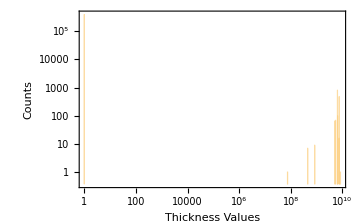
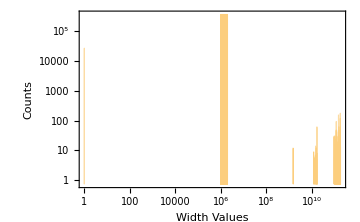
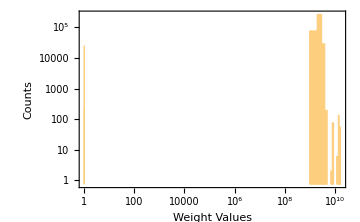
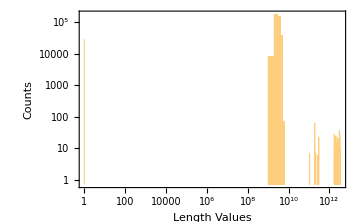

```mathematica
{Histogram[datafullwiththicknonzero[[All,10]],{10^6},ScalingFunctions->{"Log","Log"},PlotRange->Full,Frame->True,FrameLabel->{"Thickness Values","Counts"},ImageSize->Medium],Histogram[datafullwiththicknonzero[[All,9]],{10^6},ScalingFunctions->{"Log","Log"},PlotRange->Full,Frame->True,FrameLabel->{"Width Values","Counts"},ImageSize->Medium],Histogram[datafullwiththicknonzero[[All,11]],{10^9},ScalingFunctions->{"Log","Log"},PlotRange->Full,Frame->True,FrameLabel->{"Weight Values","Counts"},ImageSize->Medium],Histogram[datafullwiththicknonzero[[All,12]],{10^9},ScalingFunctions->{"Log","Log"},PlotRange->Full,Frame->True,FrameLabel->{"Length Values","Counts"},ImageSize->Medium]}
```

```mathematica
datafullnoNA=datafull/."NA"->0;
```

```mathematica
datafullnoNA[[Flatten[Position[RealDigits[datafullnoNA[[All,9]]][[All,2]],_?(4<#&)],1],9]]/=1000;
datafullnoNA[[Flatten[Position[RealDigits[datafullnoNA[[All,12]]][[All,2]],_?(8≤#&)],1],12]]/=1000;
datafullnoNA[[Flatten[Position[RealDigits[datafullnoNA[[All,11]]][[All,2]],_?(8≤#&)],1],11]]/=1000;
```

```mathematica
datafullnoNA[[Flatten[Position[datafullnoNA[[All,11]],_?Negative],1],11]]*=-1;
```

```mathematica
datafullnoNA[[Flatten[Position[RealDigits[datafullnoNA[[All,9]]][[All,2]],_?(6<#&)],1],9]]/=10^5;
datafullnoNA[[Flatten[Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(7<#&)],1],10]]/=10^8;
datafullnoNA[[Flatten[Position[RealDigits[datafullnoNA[[All,12]]][[All,2]],_?(8≤#&)],1],12]]/=10^5;
```

```mathematica
Length@Position[RealDigits[datafullnoNA[[All,12]]][[All,2]],_?(#==6&)]
Length@Position[RealDigits[datafullnoNA[[All,11]]][[All,2]],_?(#==6&)]
```

25471

39742

```mathematica
Length@datafullnoNA[[Flatten[Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(2<#&)],1],10]]
Length@datafullnoNA[[Flatten[Position[RealDigits[datafullnoNA[[All,9]]][[All,2]],_?(5≤#&)],1],9]]
Length@datafullnoNA[[Flatten[Position[RealDigits[datafullnoNA[[All,11]]][[All,2]],_?(8<#&)],1],11]]
Length@datafullnoNA[[Flatten[Position[RealDigits[datafullnoNA[[All,12]]][[All,2]],_?(8<#&)],1],12]]
```

0

0

0

«1 more identical outputs»

```mathematica
c=Flatten[Position[RealDigits[datafullnoNA[[All,12]]][[All,2]],_?(8<#&)],1];
b=Flatten[Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(5≤#&)],1];
a=Flatten[Position[RealDigits[datafullnoNA[[All,9]]][[All,2]],_?(5≤#&)],1];
```

```mathematica
Count[Table[MemberQ[a,i],{i,c}],True]
```

0

```mathematica
row=datafullnoNA[[37,9;;12]]
N@row[[3]]/(row[[1]]*row[[2]]*row[[4]])
row=datafullnoNA[[8396,9;;12]]
N@row[[3]]/(row[[1]]*row[[2]]*row[[4]])
```

{1520.,66.,2.07×10^6,274000.}

0.0000753065

{1520.,66.,2.08×10^6,2.75×10^6}

7.53951×10^-6

```mathematica
row=datafullnoNA[[15,9;;12]]
N@row[[3]]/(row[[1]]*row[[2]]*row[[4]])
```

{1220.,65.,207000.,3.42×10^6}

7.63257×10^-7

```mathematica
7.694697349869764*^-24*10^5*10^8*10^5
```

7.6947×10^-6

```mathematica
Flatten[Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(5≤#&)],1][[Flatten@Position[table,7.973733583489682*^-19]]]
Flatten[Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(5≤#&)],1][[Flatten@Position[table,7.940717777361331*^-25]]]
Flatten[Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(5≤#&)],1][[Flatten@Position[table,7.694697349869764*^-24]]]
Flatten[Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(5≤#&)],1][[Flatten@Position[table,7.275597826778928*^-21]]]
Flatten[Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(5≤#&)],1][[Flatten@Position[table,7.135721421435708*^-23]]]
Flatten[Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(5≤#&)],1][[Flatten@Position[table,7.051518679425656*^-22]]]
```

{}

{}

{}

«3 more identical outputs»

```mathematica
rowtable=datafullnoNA[[Flatten[Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(5≤#&)],1],9;;12]];
table=Table[N@i[[3]]/(i[[1]]*i[[2]]*i[[4]]),{i,rowtable}];
Length@table
table
```

0

{}

```mathematica
densities=datafull[[All,11]]/(datafull[[All,9]]*datafull[[All,10]]*datafull[[All,12]]);
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
densitieswithconvertedvalues=datafullnoNA[[All,11]]/(datafullnoNA[[All,9]]*datafullnoNA[[All,10]]*datafullnoNA[[All,12]]);
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Counts@densitieswithconvertedvalues
```

<|7.58167×10^-6→110,7.62861×10^-6→39,7.63257×10^-6→192,7.59272×10^-6→148,7.54014×10^-6→75,7.53065×10^-6→40,ComplexInfinity→50862,7.55846×10^-6→97,7.62036×10^-6→47,7.63562×10^-6→187,7.62979×10^-6→43,7.63826×10^-6→140,14776,7.48739×10^-6→7,7.48094×10^-6→5,7.47589×10^-6→18,7.48938×10^-6→6,7.46132×10^-6→7,7.36805×10^-6→7,7.46339×10^-6→12,7.4496×10^-6→11,7.42502×10^-6→32,7.49466×10^-6→6,7.40059×10^-6→4,7.46356×10^-6→4|>
 |  |  |  |

```mathematica
densitieswithconvertedvaluesallreal=densitieswithconvertedvalues/.{Indeterminate->0,ComplexInfinity->0};
Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-4&)];
Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-6&)];
```

```mathematica
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-4&)],1],12]]*=10;
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-6&)],1],11]]*=10;
```

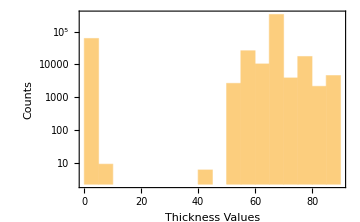
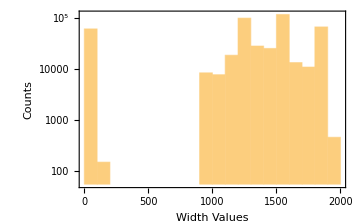
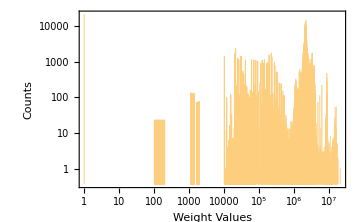
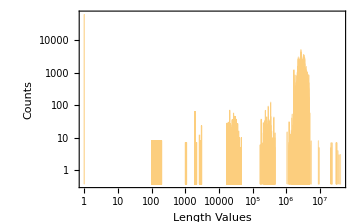

```mathematica
{Histogram[datafullnoNA[[All,10]],ScalingFunctions->"Log",PlotRange->Automatic,Frame->True,FrameLabel->{"Thickness Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,9]],ScalingFunctions->"Log",PlotRange->Automatic,Frame->True,FrameLabel->{"Width Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,11]],{10^2},ScalingFunctions->{"Log","Log"},PlotRange->Full,Frame->True,FrameLabel->{"Weight Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,12]],{10^2},ScalingFunctions->{"Log","Log"},PlotRange->Full,Frame->True,FrameLabel->{"Length Values","Counts"},ImageSize->Medium]}
```

```mathematica
Counts@densitieswithconvertedvalues
```

<|7.58167×10^-6→102,7.62861×10^-6→39,7.63257×10^-7→8,7.59272×10^-6→134,7.54014×10^-6→75,0.0000753065→8,ComplexInfinity→50862,7.55846×10^-6→97,7.63257×10^-6→184,7.62036×10^-6→47,7.63562×10^-6→181,7.62979×10^-6→43,17557,7.48094×10^-6→5,7.47589×10^-6→18,7.48938×10^-6→6,7.46132×10^-6→7,7.36805×10^-6→7,7.46339×10^-6→12,7.4496×10^-6→11,7.42502×10^-6→32,7.44009×10^-7→6,7.49466×10^-6→6,7.40059×10^-6→4,0.0000746356→4|>
 |  |  |  |

```mathematica
RealDigits@7.558461594214153*^-6
RealDigits@0.00007530646456885412
```

{{7,5,5,8,4,6,1,5,9,4,2,1,4,1,5,3},-5}

{{7,5,3,0,6,4,6,4,5,6,8,8,5,4,1,2},-4}

```mathematica
densitieswithconvertedvalues=datafullnoNA[[All,11]]/(datafullnoNA[[All,9]]*datafullnoNA[[All,10]]*datafullnoNA[[All,12]]);
densitieswithconvertedvaluesallreal=densitieswithconvertedvalues/.{Indeterminate->0,ComplexInfinity->0};
Length@Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-5&)]
Length@densitieswithconvertedvaluesallreal[[Flatten@Position[densitieswithconvertedvalues,_?(10^(-6)<#<10^(-5)&)]]]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

397666

Less::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

397666

```mathematica
RealDigits@7.566204287515763*^-11
RealDigits@7.429082120934902*^-8
RealDigits@0.7597403069496246
RealDigits@0.0007618610082215906
RealDigits@0.00007566204287515763
RealDigits@0.007827510140183591
RealDigits@0.07229982293920913
RealDigits@7.938398031277288*^-10
RealDigits@7.940717777361331*^-12
RealDigits@8.655928986758592*^-9
```

{{7,5,6,6,2,0,4,2,8,7,5,1,5,7,6,3},-10}

{{7,4,2,9,0,8,2,1,2,0,9,3,4,9,0,2},-7}

{{7,5,9,7,4,0,3,0,6,9,4,9,6,2,4,6},0}

{{7,6,1,8,6,1,0,0,8,2,2,1,5,9,0,6},-3}

{{7,5,6,6,2,0,4,2,8,7,5,1,5,7,6,3},-4}

{{7,8,2,7,5,1,0,1,4,0,1,8,3,5,9,2},-2}

{{7,2,2,9,9,8,2,2,9,3,9,2,0,9,1,3},-1}

{{7,9,3,8,3,9,8,0,3,1,2,7,7,2,8,8},-9}

{{7,9,4,0,7,1,7,7,7,7,3,6,1,3,3,1},-11}

{{8,6,5,5,9,2,8,9,8,6,7,5,8,5,9,3},-8}

```mathematica
Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-10&)];
Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-7&)];
Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==0&)];
Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-3&)];
Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-4&)];
```

```mathematica
Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-2&)];
Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-1&)];
```

```mathematica
Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-9&)];
Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-11&)];
```

```mathematica
Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-8&)];
```

```mathematica
row=datafullnoNA[[1996,9;;12]]
N@row[[3]]/(row[[1]]*row[[2]]*row[[4]])
row=datafullnoNA[[7352,9;;12]]
N@row[[3]]/(row[[1]]*row[[2]]*row[[4]])
row=datafullnoNA[[163,9;;12]]
N@row[[3]]/(row[[1]]*row[[2]]*row[[4]])
row=datafullnoNA[[73901,9;;12]]
N@row[[3]]/(row[[1]]*row[[2]]*row[[4]])
row=datafullnoNA[[1996,9;;12]]
N@row[[3]]/(row[[1]]*row[[2]]*row[[4]])
row=datafullnoNA[[156302,9;;12]]
N@row[[3]]/(row[[1]]*row[[2]]*row[[4]])
row=datafullnoNA[[12436,9;;12]]
N@row[[3]]/(row[[1]]*row[[2]]*row[[4]])
row=datafullnoNA[[45082,9;;12]]
N@row[[3]]/(row[[1]]*row[[2]]*row[[4]])
row=datafullnoNA[[152187,9;;12]]
N@row[[3]]/(row[[1]]*row[[2]]*row[[4]])
row=datafullnoNA[[249691,9;;12]]
N@row[[3]]/(row[[1]]*row[[2]]*row[[4]])
```

{1290.,87.,20.5,2.41×10^6}

7.57928×10^-11

{1530.,65.,13750,1.83×10^6}

7.55521×10^-8

{1220.,65.,2.12×10^6,35.}

0.763826

{1860.,65.,2.1×10^6,22750}

0.000763504

{1290.,87.,20.5,2.41×10^6}

7.57928×10^-11

{1840.,65.,1.49×10^7,19000.}

0.00655694

{1390.,65.,203000.,29.5}

0.0761633

{1540.,65.,1.5,21000.}

7.13572×10^-10

{1210.,65.,1.5,3.87×10^6}

4.92812×10^-12

{1230.,65.,2.,2890.}

8.65593×10^-9

```mathematica
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-10&)],1],11]]*=10^6;
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-7&)],1],11]]*=10^2;
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==0&)],1],12]]*=10^5;
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-3&)],1],12]]*=10^2;
```

```mathematica
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-4&)],1],11]]/=10;
```

```mathematica
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-2&)],1],12]]*=10^3;
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-1&)],1],11]]*=10;
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-1&)],1],12]]*=10^5;
```

```mathematica
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-9&)],1],11]]*=10^6;
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-9&)],1],12]]*=10^2;
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-11&)],1],11]]*=10^6;
```

```mathematica
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-8&)],1],11]]*=10^6;
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-8&)],1],12]]*=10^3;
```

```mathematica
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-4&)],1],12]]*=10;
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-6&)],1],11]]*=10;
```

```mathematica
Length@Join[Position[densitieswithconvertedvaluesallreal,0],Position[densitieswithconvertedvaluesallreal,0.]]
Length@Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#!=-5&)]
```

61530

62588

```mathematica
densitieswithconvertedvalues=datafullnoNA[[All,11]]/(datafullnoNA[[All,9]]*datafullnoNA[[All,10]]*datafullnoNA[[All,12]]);
densitieswithconvertedvaluesallreal=densitieswithconvertedvalues/.{Indeterminate->0,ComplexInfinity->0};
Length@Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-5&)]
Length@densitieswithconvertedvaluesallreal[[Flatten@Position[densitieswithconvertedvalues,_?(10^(-6)<#<10^(-5)&)]]]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

397666

Less::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

397666

```mathematica
ReverseSortBy[Last@*Total]@Counts@densitieswithconvertedvaluesallreal[[Complement[Flatten@Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#!=-5&)],Flatten@Join[Position[densitieswithconvertedvaluesallreal,0],Position[densitieswithconvertedvaluesallreal,0.]]]]]
```

Last::normal: Nonatomic expression expected at position 1 in Last[7].

<|1.47048→7|>

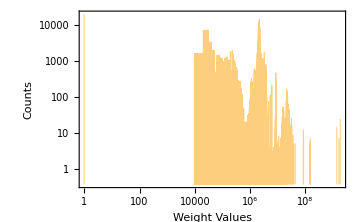
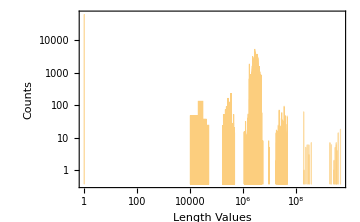
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Histogram[datafullnoNA[[All,10]],ScalingFunctions->"Log",PlotRange->Automatic,Frame->True,FrameLabel->{"Thickness Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,9]],ScalingFunctions->"Log",PlotRange->Automatic,Frame->True,FrameLabel->{"Width Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,11]],{10^4},ScalingFunctions->{"Log","Log"},PlotRange->Full,Frame->True,FrameLabel->{"Weight Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,12]],{10^4},ScalingFunctions->{"Log","Log"},PlotRange->Full,Frame->True,FrameLabel->{"Length Values","Counts"},ImageSize->Medium]}
```

```mathematica
unacceptabledensitypos=Complement[Complement[Range@Length@densitieswithconvertedvaluesallreal,Flatten@Position[densitieswithconvertedvaluesallreal,_?(7*10^-6<#<8.5*10^-6&)]],Flatten@Join[Position[densitieswithconvertedvaluesallreal,0],Position[densitieswithconvertedvaluesallreal,0.]]];
```

```mathematica
datafullnoNA[[All,9]]=ReplacePart[datafullnoNA[[All,9]],{Partition[unacceptabledensitypos,1]->"NA"}];
datafullnoNA[[All,10]]=ReplacePart[datafullnoNA[[All,10]],{Partition[unacceptabledensitypos,1]->"NA"}];
datafullnoNA[[All,11]]=ReplacePart[datafullnoNA[[All,11]],{Partition[unacceptabledensitypos,1]->"NA"}];
datafullnoNA[[All,12]]=ReplacePart[datafullnoNA[[All,12]],{Partition[unacceptabledensitypos,1]->"NA"}];
```

```mathematica
(* Export["datafull_manipulated.csv",datafullnoNA] *)
```

datafull_manipulated.csv